```mathematica
<<Combinatorica`
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

```mathematica
h={{1,2},{2,2},{2,3},{2,4},{3,3},{3,2},{3,2},{4,4},{4,3},{4,2}};
```

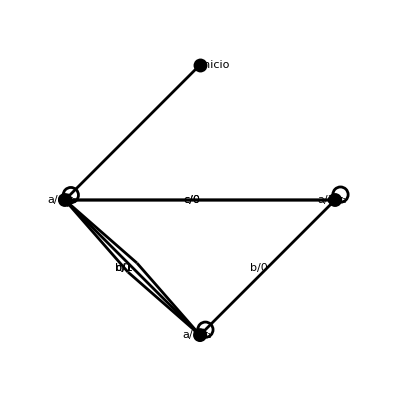

```mathematica
ShowGraph[G=SetGraphOptions[FromOrderedPairs[h],VertexColors->Black,EdgeColoring->Gray],VertexLabel->{"inicio","σ_0","σ_1","σ_2"},EdgeLabel->{"","a/0","b/1","c/0","a/1","b/1","c/1","a/1","b/0","c/0"},PlotRange->0.1]
```

```mathematica
(*Se puede apreciar que con el comando ShowGraph se da una sobreposición de las etiquetas de las aristas múltiples*)
(*Otra opción es usar Graph con una única arista por cada conjunto de lados múltiples y etiquetar con todos los símbolos entrada/salida*)
```

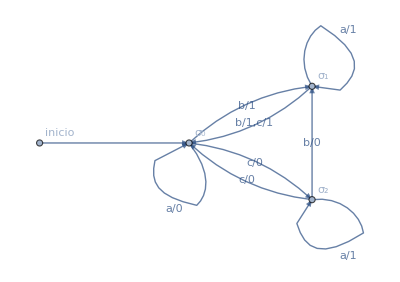

```mathematica
Graph[{inicio->Subscript[σ, 0],Subscript[σ, 0]->Subscript[σ, 0],Subscript[σ, 0]->Subscript[σ, 1],Subscript[σ, 0]->Subscript[σ, 2],Subscript[σ, 1]->Subscript[σ, 1],Subscript[σ, 1]->Subscript[σ, 0],Subscript[σ, 2]->Subscript[σ, 2],Subscript[σ, 2]->Subscript[σ, 1],Subscript[σ, 2]->Subscript[σ, 0]},EdgeLabels->{Subscript[σ, 0]->Subscript[σ, 0]->"a/0",Subscript[σ, 0]->Subscript[σ, 1]->"b/1",Subscript[σ, 0]->Subscript[σ, 2]->"c/0",Subscript[σ, 1]->Subscript[σ, 1]->"a/1",Subscript[σ, 1]->Subscript[σ, 0]->"b/1,c/1",Subscript[σ, 2]->Subscript[σ, 2]->"a/1",Subscript[σ, 2]->Subscript[σ, 1]->"b/0",Subscript[σ, 2]->Subscript[σ, 0]->"c/0"},VertexLabels->"Name",ImagePadding->10,EdgeStyle->Arrowheads[Medium],EdgeShapeFunction->"Arrow"]
```